## Set Directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

Position extractor by names

```mathematica
ExtractorByNames[labels_,varlabels_]:=Block[{notfoundQ,xpos,ypos},
notfoundQ=Flatten[Position[labels,varlabels[[1]]]]=={};
If[notfoundQ,
Print["Not able to find the provided label = ",varlabels[[1]] ;]
,
xpos= Flatten[Position[labels,varlabels[[1]]]][[1]];
];
notfoundQ=Flatten[Position[labels,varlabels[[2]]]]=={};
If[notfoundQ,
Print["Not able to find the provided label = ",varlabels[[1]] ;]
,
ypos= Flatten[Position[labels,varlabels[[2]]]][[1]];
];
Return[{xpos,ypos}];
];
```

Loading RK raw data

```mathematica
rkrawdata=Import["ElastoPlasticRKdata.txt","Data"];
rklabels=rkrawdata[[1]];
rkdata = Drop[rkrawdata,1];
```

```mathematica
rklabels
```

{radius,u,sigma_rr,sigma_tt,sigma_zz,eps_rr,eps_tt,eps_zz,eps_p_rr,eps_p_tt,eps_p_zz}

Loading Paraview data

```mathematica
pvrawdata=Import["ElastoPlasticIntPoints-CPU.csv","Data"];
pvlabels=pvrawdata[[1]]
pvdata = Drop[pvrawdata,1];
```

{FailureType,Displacement:0,Displacement:1,Displacement:2,Stress:0,Stress:1,Stress:2,Stress:3,Stress:4,Stress:5,Stress:6,Stress:7,Stress:8,Strain:0,Strain:1,Strain:2,Strain:3,Strain:4,Strain:5,Strain:6,Strain:7,Strain:8,StrainPlastic:0,StrainPlastic:1,StrainPlastic:2,StrainPlastic:3,StrainPlastic:4,StrainPlastic:5,StrainPlastic:6,StrainPlastic:7,StrainPlastic:8,vtkValidPointMask,arc_length,Points:0,Points:1,Points:2}

Applying radius shift because plot over line start on rw (?_?)

```mathematica
rw=0.1;
rpos=ExtractorByNames[pvlabels,{"arc_length","arc_length"}][[1]];
pvdata[[All,{rpos}]]+=rw;
```

```mathematica
pvlabels
```

{FailureType,Displacement:0,Displacement:1,Displacement:2,Stress:0,Stress:1,Stress:2,Stress:3,Stress:4,Stress:5,Stress:6,Stress:7,Stress:8,Strain:0,Strain:1,Strain:2,Strain:3,Strain:4,Strain:5,Strain:6,Strain:7,Strain:8,StrainPlastic:0,StrainPlastic:1,StrainPlastic:2,StrainPlastic:3,StrainPlastic:4,StrainPlastic:5,StrainPlastic:6,StrainPlastic:7,StrainPlastic:8,vtkValidPointMask,arc_length,Points:0,Points:1,Points:2}

## Plots controls

```mathematica
colors=ColorData[81,"ColorList"];
```

```mathematica
fonts=16;
labelfonts=16;
methodlabels = {Style["Runge-Kutta",colors[[2]],fonts],Style["FE",colors[[1]],fonts]};
grules={PlotRange->All,Frame->True,FrameStyle->Directive[Black,fonts], GridLines->Automatic,PlotStyle->{colors[[2]],colors[[1]]},Joined->{True,False}, ImageSize->500,PlotLegends->Placed[LineLegend[methodlabels,LegendLabel->Style[".08Approximations :",Black,fonts],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],{0.6,0.2}],PlotMarkers->Automatic};
```

Gathering data for RK

```mathematica
dsigmar=rkdata[[All,ExtractorByNames[rklabels,{"radius","sigma_rr"}]]];
dsigmat=rkdata[[All,ExtractorByNames[rklabels,{"radius","sigma_tt"}]]];
depsr=rkdata[[All,ExtractorByNames[rklabels,{"radius","eps_rr"}]]];
depst=rkdata[[All,ExtractorByNames[rklabels,{"radius","eps_tt"}]]];
depspr=rkdata[[All,ExtractorByNames[rklabels,{"radius","eps_p_rr"}]]];
depspt=rkdata[[All,ExtractorByNames[rklabels,{"radius","eps_p_tt"}]]];
```

Gathering data from CPU approximation

```mathematica
dpvsigmar=pvdata[[All,ExtractorByNames[pvlabels,{"arc_length","Stress:0"}]]];
dpvsigmat=pvdata[[All,ExtractorByNames[pvlabels,{"arc_length","Stress:4"}]]]; 
dpvepsr=pvdata[[All,ExtractorByNames[pvlabels,{"arc_length","Strain:0"}]]];
dpvepst=pvdata[[All,ExtractorByNames[pvlabels,{"arc_length","Strain:4"}]]];
dpvepspr=pvdata[[All,ExtractorByNames[pvlabels,{"arc_length","StrainPlastic:0"}]]];
dpvepspt=pvdata[[All,ExtractorByNames[pvlabels,{"arc_length","StrainPlastic:4"}]]];
```

Rendering plots

```mathematica
gcompsigmar=ListPlot[{dsigmar,dpvsigmar},grules, FrameLabel->{Style[".08Radius [m] ",Black,fonts],Style["σ_rr",Black,fonts]},FrameStyle->Directive[Black,FontSize->labelfonts],AspectRatio->1];
gcompsigmat=ListPlot[{dsigmat,dpvsigmat},grules, FrameLabel->{Style[".08Radius [m] ",Black,fonts],Style["σ_θθ",Black,fonts]},FrameStyle->Directive[Black,FontSize->labelfonts],AspectRatio->1];
gcompepsr=ListPlot[{depsr,dpvepsr},grules, FrameLabel->{Style[".08Radius [m] ",Black,fonts],Style["ϵ_rr",Black,fonts]},FrameStyle->Directive[Black,FontSize->labelfonts],AspectRatio->1];
gcompepst=ListPlot[{depst,dpvepst},grules, FrameLabel->{Style[".08Radius [m] ",Black,fonts],Style["ϵ_θθ",Black,fonts]},FrameStyle->Directive[Black,FontSize->labelfonts],AspectRatio->1];
gcompepspr=ListPlot[{dpvepspr,depspr},grules, FrameLabel->{Style[".08Radius [m] ",Black,fonts],Style["(ϵ^p)_rr",Black,fonts]},FrameStyle->Directive[Black,FontSize->labelfonts],AspectRatio->1];
gcompepspt=ListPlot[{dpvepspt,depspt},grules, FrameLabel->{Style[".08Radius [m] ",Black,fonts],Style["(ϵ^p)_θθ",Black,fonts]},FrameStyle->Directive[Black,FontSize->labelfonts],AspectRatio->1];
```

## Exporting plots

```mathematica
imageres=200;
RedenderplotsQ=True;
If[RedenderplotsQ,
Export["elastoplastic_comp_u.png",gcompu,ImageResolution-> imageres];
Export["elastoplastic_comp_sigma_r.png",gcompsigmar,ImageResolution-> imageres];
Export["elastoplastic_comp_sigma_t.png",gcompsigmat,ImageResolution-> imageres];
Export["elastoplastic_comp_eps_r.png",gcompepsr,ImageResolution-> imageres];
Export["elastoplastic_comp_eps_t.png",gcompepst,ImageResolution-> imageres];
Export["elastoplastic_comp_eps_p_r.png",gcompepspr,ImageResolution-> imageres];
Export["elastoplastic_comp_eps_p_t.png",gcompepspt,ImageResolution-> imageres];
];
```

## BC data for RK approximation

```mathematica
Print["ur and σr at Re = ",pvdata[[All,ExtractorByNames[pvlabels,{"Displacement:0","Stress:0"}]]][[-1]]]
```

ur and σr at Re = {0,-0.00622045}

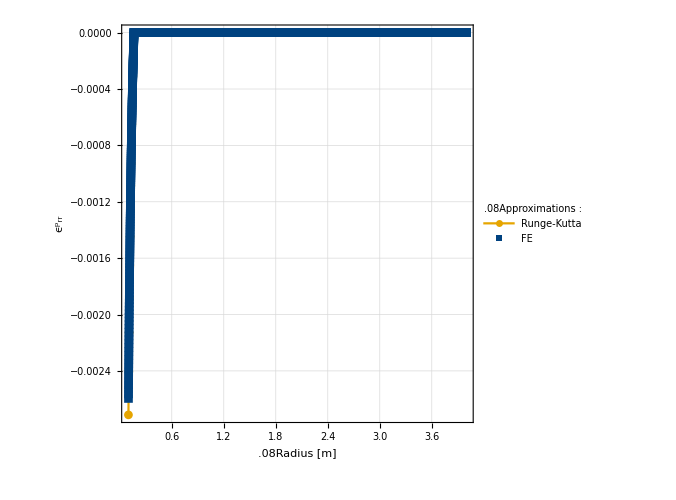

```mathematica
gcompepspr
```